## Solving system equation

```mathematica
Quit[]
```

```mathematica
Dgg=gg'[r]==(gg[r]^9 (w^6 (r^2 α+η) ϕ[r]^6+w^4 NN[r]^2 ϕ[r]^4 (-2 k+m^2 r^2 ϕ[r]^2))-w^2 gg[r]^7 ϕ[r]^2 (w^4 η ϕ[r]^4+2 NN[r]^4 (-2 k+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^2 NN[r]^2 ϕ[r]^2 (-2 k+(r^2 α+η) ϕ'[r]^2))+gg[r]^5 NN[r]^2 ϕ'[r]^2 (NN[r]^4 (-2 k+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^4 η ϕ[r]^3 (ϕ[r]+4 r ϕ'[r])-w^2 NN[r]^2 ϕ[r]^2 (4 k+(r^2 α+η) ϕ'[r]^2))+3 η gg[r] NN[r]^6 ϕ'[r]^5 (ϕ'[r]+4 r ϕ''[r])+gg[r]^3 NN[r]^4 ϕ'[r]^3 (NN[r]^2 (2 k ϕ'[r]+(r^2 α+η) ϕ'[r]^3)+w^2 η ϕ[r] (12 r ϕ'[r]^2-ϕ[r] (3 ϕ'[r]+28 r ϕ''[r]))))/(2 r (gg[r]^6 (2 k w^4 NN[r]^2 ϕ[r]^4-w^6 η ϕ[r]^6)+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (-4 k NN[r]^2+3 w^2 η ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (2 k NN[r]^2-19 w^2 η ϕ[r]^2) ϕ'[r]^4+9 η NN[r]^6 ϕ'[r]^6));

DNN=NN'[r]==(NN[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2) (gg[r]^6 (w^4 (r^2 α+η) ϕ[r]^4+w^2 NN[r]^2 ϕ[r]^2 (2 k-m^2 r^2 ϕ[r]^2))+9 η NN[r]^4 ϕ'[r]^4-gg[r]^4 (2 k w^2 NN[r]^2 ϕ[r]^2+NN[r]^4 (2 k-m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^4 η ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))-gg[r]^2 NN[r]^2 ϕ'[r] (NN[r]^2 (-2 k ϕ'[r]+(r^2 α+η) ϕ'[r]^3)+4 w^2 η ϕ[r] (-4 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r])))))/(2 r (gg[r]^6 (2 k w^4 NN[r]^2 ϕ[r]^4-w^6 η ϕ[r]^6)+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (-4 k NN[r]^2+3 w^2 η ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (2 k NN[r]^2-19 w^2 η ϕ[r]^2) ϕ'[r]^4+9 η NN[r]^6 ϕ'[r]^6));

DDPhi=ϕ''[r]==(-w^6 gg[r]^11 (w^2 (r^2 α+η)-m^2 r^2 NN[r]^2) ϕ[r]^7+9 η NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7+w^6 gg[r]^8 ϕ[r]^6 gg'[r] (-2 r w^2 η ϕ[r]+(r^2 α+η) NN[r]^2 ϕ'[r])+w^4 gg[r]^9 ϕ[r]^5 (w^4 η ϕ[r]^2-w^2 NN[r] ϕ[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r]+3 NN[r]^2 (w^2 (r^2 α+η)-m^2 r^2 NN[r]^2) ϕ'[r]^2)+w^2 gg[r]^7 NN[r] ϕ[r]^3 ϕ'[r] (w^4 η ϕ[r]^3 NN'[r]-3 w^4 η ϕ[r]^2 (3 NN[r]+2 r NN'[r]) ϕ'[r]+w^2 NN[r] ϕ[r] (4 r w^2 η+6 r α NN[r]^2+3 (r^2 α+η) NN[r] NN'[r]) ϕ'[r]^2+3 NN[r]^3 (-w^2 (r^2 α+η)+m^2 r^2 NN[r]^2) ϕ'[r]^3)+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (70 r w^2 η ϕ[r]^2 gg'[r] NN'[r]+3 (r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (15 ϕ[r] gg'[r]-38 r gg'[r] ϕ'[r]-4 r ϕ[r] gg''[r]))-gg[r]^2 NN[r]^5 ϕ'[r]^5 (58 r w^2 η ϕ[r]^2 gg'[r] NN'[r]+(r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (23 ϕ[r] gg'[r]-16 r gg'[r] ϕ'[r]-2 r ϕ[r] gg''[r]))+w^4 gg[r]^6 NN[r] ϕ[r]^4 ϕ'[r] (2 r w^2 η ϕ[r]^2 gg'[r] NN'[r]-3 (r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (-ϕ[r] gg'[r]+24 r gg'[r] ϕ'[r]+2 r ϕ[r] gg''[r]))-η gg[r] NN[r]^6 ϕ'[r]^5 (4 r w^2 ϕ[r]^2 gg'[r]^2+3 NN[r] ϕ'[r]^2 (3 NN'[r]+2 r NN''[r]))-gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (8 r w^6 η ϕ[r]^5 gg'[r]^2-w^4 η NN[r] ϕ[r]^2 (19 NN[r]+24 r NN'[r]) ϕ'[r]^3+3 w^2 NN[r]^3 ϕ[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r]^4+NN[r]^4 (-w^2 (r^2 α+η)+m^2 r^2 NN[r]^2) ϕ'[r]^5+w^4 η ϕ[r]^3 ϕ'[r]^2 (28 r NN'[r]^2+NN[r] (23 NN'[r]+14 r NN''[r])))+gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 r w^4 η ϕ[r]^4 gg'[r]^2+w^2 η NN[r] ϕ[r] (-11 NN[r]+14 r NN'[r]) ϕ'[r]^3+NN[r]^2 (-4 r w^2 η+2 r α NN[r]^2+(r^2 α+η) NN[r] NN'[r]) ϕ'[r]^4+w^2 η ϕ[r]^2 ϕ'[r]^2 (-4 r NN'[r]^2+NN[r] (31 NN'[r]+20 r NN''[r]))))/(gg[r] NN[r]^2 (w^6 (r^2 α+η) gg[r]^8 ϕ[r]^6-2 r w^6 η gg[r]^5 ϕ[r]^6 gg'[r]+2 r w^2 η gg[r] NN[r]^4 ϕ[r]^2 gg'[r] ϕ'[r]^4+3 η NN[r]^5 (NN[r]+2 r NN'[r]) ϕ'[r]^6-w^4 gg[r]^6 ϕ[r]^4 (w^2 η ϕ[r]^2-12 r w^2 η ϕ[r] ϕ'[r]+3 (r^2 α+η) NN[r]^2 ϕ'[r]^2)+w^2 gg[r]^4 NN[r] ϕ[r]^2 ϕ'[r]^2 (42 r w^2 η ϕ[r]^2 NN'[r]+3 (r^2 α+η) NN[r]^3 ϕ'[r]^2+w^2 η NN[r] ϕ[r] (9 ϕ[r]-16 r ϕ'[r]))-gg[r]^2 NN[r]^3 ϕ'[r]^4 (16 r w^2 η ϕ[r]^2 NN'[r]+(r^2 α+η) NN[r]^3 ϕ'[r]^2+w^2 η NN[r] ϕ[r] (11 ϕ[r]-4 r ϕ'[r]))));
```

### Solving

```mathematica
Clear[rMin,rMax, ϕ0,r, η,α,k,mS]
```

```mathematica
SeidelEqsList={};
SeidelEqsListH={};
SeidelBCList={};
SeidelBCListH={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];

AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

AppendTo[SeidelBCList,{NN[rMin]==1.,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];
```

## G_eff

```mathematica
Bs={0.03,1.121058474193216440,20,30,-0.3,10^-8}; (* caso linea negra, Fig 3 izquierda *)
```

```mathematica
Bs={0.03,1.116036581602133000,30,30,0,10^-8}; (* E-KG *)
```

```mathematica
Bs={0.015,1.054140552042320860,28,30,-0.3,10^-8}; (* caso linea azul, Fig 3 izquierda *)
```

0.948119

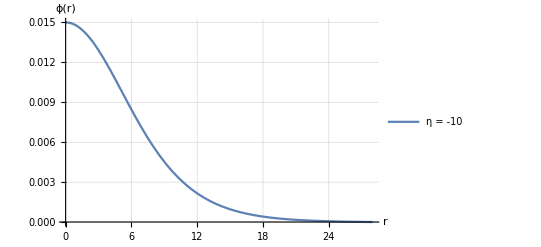

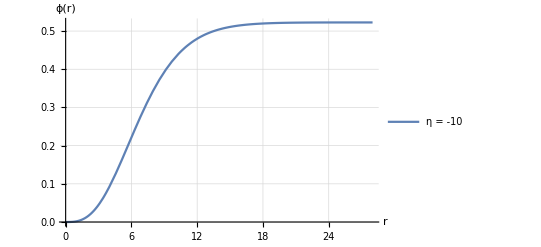

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=Bs[[1]];
w=Bs[[2]];
rMax=Bs[[3]];
rMin=Bs[[6]];

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}, MaxSteps->10^6];

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]

M[r_]:=1/2 r (1-1/gg[r]^2);

Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
M95=0.95Evaluate[M[rMax]/.s][[1]]; (* masa física *)
MM[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s];
rad=Last[FindRoot[MM[r]==M95,{r,rMin+0.5,rMax}]];
Print[rad];
Print["masa95 = ", M95];
```

r→13.181

masa95 = 0.496469

```mathematica
(* sin el reescalamiento *)
```

0.522599

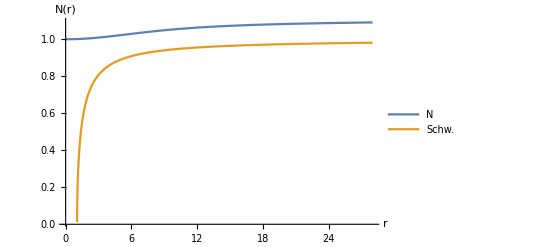

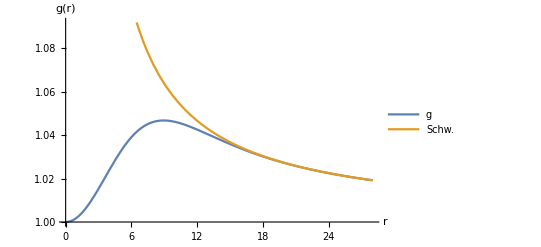

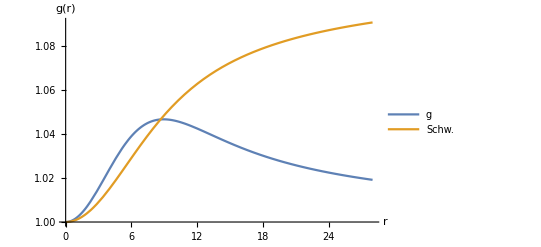

```mathematica
Masa=MM[rMax][[1]]
Plot[{Evaluate[NN[r]/.s],Sqrt[(1-(2Masa)/r)]},{r,rMin,rMax},Background->White,PlotLegends->Placed[{"N ","Schw."},{0.85,0.56}],AxesLabel->{"r","N(r)"},AxesOrigin->{0,0},PlotRange->All]

Plot[{Evaluate[gg[r]/.s],Sqrt[(1-(2Masa)/r)^-1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g ","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]

Plot[{Evaluate[gg[r]/.s],Evaluate[NN[r]/.s]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g ","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]
```

```mathematica
(* Reescalando *)
```

```mathematica
Clear[rMin,rTest,α,w,ϕ0,mS,k,η]
```

```mathematica
SeidelEqsList={};
SeidelBCList={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];
AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

AppendTo[SeidelBCList,{NN[rMin]==1*B[[1,1,1,2]],gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];
```

```mathematica
w2
```

0.948119

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

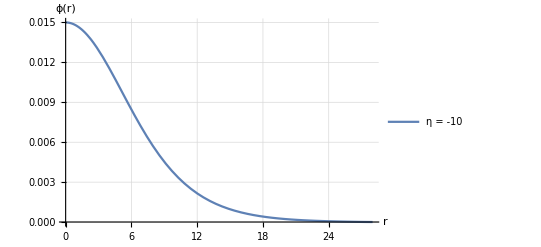

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=SetPrecision[Bs[[1]],prec];
w= w2(*w2*);(*0.8967355292683497*)
rMax=SetPrecision[Bs[[3]],prec](*SetPrecision[Bs[[3]],prec]*)(*28*);
rMin=10^-6(*SetPrecision[Bs[[6]],prec]*);

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

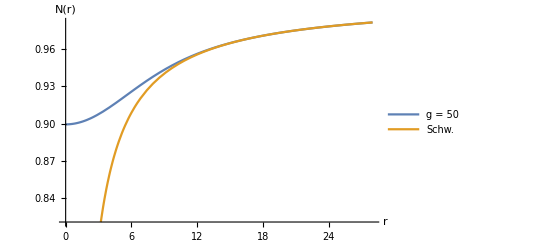

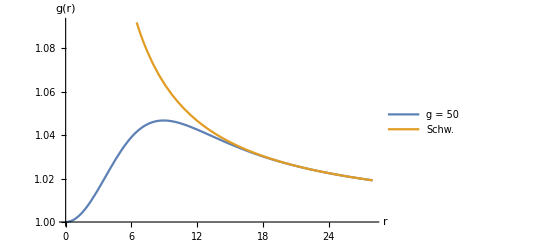

```mathematica
(* comprobando que se pega a Schw *)
Plot[{Evaluate[NN[r]/.s],Sqrt[(1-(2Masa)/r)]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.56}],
PlotRange->Automatic,AxesLabel->{"r","N(r)"}]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.s],Sqrt[(1-(2Masa)/r)^-1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]
```

```mathematica
Funcg={};
Do[AppendTo[Funcg,{r,Evaluate[gg[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
FuncN={};
Do[AppendTo[FuncN,{r,Evaluate[NN[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
Funcsigma={};
Do[AppendTo[Funcsigma,{r,Evaluate[φ[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
FuncM={};
Do[AppendTo[FuncM,{r,Evaluate[M[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
Export["FuncgEKG.dat",Funcg]
Export["FuncNEKG.dat",FuncN]
Export["FuncMEKG.dat",FuncM]
Export["FuncsigmaEKG.dat",Funcsigma]
```

FuncgEKG.dat

FuncNEKG.dat

FuncMEKG.dat

FuncsigmaEKG.dat

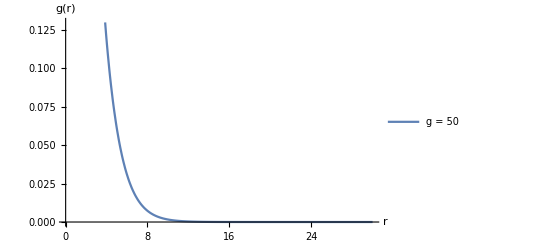

```mathematica
Plot[{Abs[Evaluate[gg[r]/.s]-Sqrt[(1-(2Masa)/r)^-1]]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]
```

Definiendo  G_eff/G-1

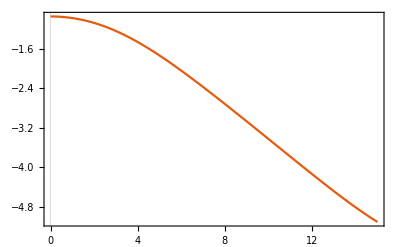

```mathematica
Van[r_]:=Abs[(gg[r]^2 NN[r]^2)/(gg[r]^2 NN[r]^2+120π η(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2))-1];(*|Subscript[G, N]/G-1|*)

B=Plot[Evaluate[Log10@Van[r]/.s],{r,rMin,15(*rMax*)}, PlotRange->All,AxesOrigin->{0,0},PlotTheme->"Scientific"](*para rho=0.03, el radio máximo es 15 *)
```

Mostrando el punto r_95 y el límite

```mathematica
radLim=Last@FindRoot[Evaluate[Log10@Van[r]/.s][[1]]==-4.327902142064283,{r,10}] (* calculando el radio límite *)
```

r→12.5555

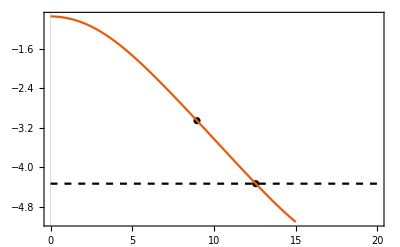

```mathematica
A=ListPlot[{{rad[[2]],Log10@ (Evaluate[Van[r]/.s]/.r-> rad[[2]])[[1]]},{radLim[[2]],Log10@( Evaluate[Van[r]/.s]/.r-> radLim[[2]])[[1]]}},PlotTheme->"Scientific",PlotStyle->{Red,Black}];

c=Plot[y=-4.327902142064283,{x,rMin,(*15*) rMax},PlotStyle-> {{Dashed,Black}}];

Show[{A,B,c},PlotRange-> {{0,(*15*) rMax},Automatic},AxesOrigin-> {0,0}]
```

## Lente fuerte implementación trabajo de Colima

```mathematica
(*
z= r0/r ;

para valores pequeños de z se debe pegar a Schwarschild y para z grandes debe ser diferente
 
*)
```

```mathematica
(*A=Plot[{V[z,rMax-10]},{z,10^-5,1}] (* diverge pq interpola fuera del valor *);*)
(*
AG=Plot[{VG[z,8.747638814268768]},{z,10^-5,1},PlotStyle->Red,AxesOrigin->{0,0},PlotTheme->"Scientific",PlotRange->All];
B=Plot[{z^2-2Masa z^3/8.747638814268768},{z,0,1},PlotStyle->Gray,PlotRange->All];
Show[{AG,B},ImageSize->600]
*)
```

### checking with Schwarzschild

```mathematica
Quit[];
```

```mathematica
ClearAll[NN,gg,z,r0,nlm,VG,sigma,delta,rh0,PotAnalit,Analit,Masa,rMax,radio95,Nfun,gfun,r]
```

```mathematica
radio95=3;
rMax=30;
Masa=1(*0.6472955723214572*);
```

```mathematica
Nfun[r_]:=√(1-(2 Masa)/r); gfun[r_]:=√((1-(2 Masa)/r)^-1);
datNfunc={};
Do[AppendTo[datNfunc,{r,Nfun[r]}],{r,radio95,rMax}];
NNInt=Interpolation[datNfunc]/.Equal-> Rule;

datgfunc={};
Do[AppendTo[datgfunc,{r,gfun[r]}],{r,radio95,rMax}];
ggInt=Interpolation[datgfunc]/.Equal-> Rule;

s={NNInt, ggInt}
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
With[{NN=s[[1]],gg=s[[2]]},
(*V[z_,r0_]:=z^2 1/gg[r0/z]-NN[r0]/(gg[r0/z]NN[r0/z])+NN[r0];*) (* diverge pq interpola fuera del valor *)

VG[z_,r0_]:=Piecewise[{{z^2 1/gg[r0/z]^2-NN[r0]^2/(gg[r0/z]^2 NN[r0/z]^2)+NN[r0]^2,r0/z<=rMax},{z^2-(2Masa)/r0 z^3,r0/z>rMax}}];
]

vs[r0_]:=Module[{r0v=r0},
(* Generating data *)
data={};
Do[AppendTo[data,{z,VG[z,r0v]}],{z,10^-5,1,0.001}];

(* Fit v1,....,v6 *)
nlm=NonlinearModelFit[data,v1 x+v2 x^2+v3 x^3+v4 x^4+v5 x^5+v6 x^6,{v1,v2,v3,v4,v5,v6},x];

(* checking *)
(*
Print[Grid[{{
ListPlot[{nlm["FitResiduals"]},BaseStyle->14, FrameLabel->{"points","Residuals"},PlotRange->All,PlotTheme->{"Scientific"},ImageSize->400,Filling->Axis],

Show[{ListPlot[{data},PlotTheme->{"Scientific"},BaseStyle->14, FrameLabel->{"z","V(z)"},ImageSize->400,PlotRange->All,PlotLegends->Placed[{"data","Fit"},Automatic]],Plot[nlm[x],{x,0,1},PlotLegends->Placed[{"Fit"},Automatic]]}]
}},Alignment->{{Left,Right}}]
];
*)

Return[nlm["BestFitParameters"]]
]

(**)
rho[r0_]:=Module[{r0v=r0},
sigma[n_]:=√π Gamma[n/2+1/2]/Gamma[n/2];
v=vs[r0v];
(* se definió desde n=1 to 6*)
rh0=Sum[v[[n,2]]sigma[n]z^n,{n,1,6}];

Return[rh0]
]

(* Definiendo el angulo *)
ang[r0_]:=Module[{r0v=r0},
delta=π(√(π/(2(rho[r0v]/.z-> 1)))-1);
Return[delta]
]
```

```mathematica
PotAnalit[z_,r0_]:=z^2-(2Masa)/r0 z^3;
Analit[r0_]:=π(√(1/(1-(8Masa)/(π r0)))-1); (* paper*)
```

Calculando ángulo vs

```mathematica
Datos={} (* la integral es integrando hasta una r0 sucesivamente y se guarda en Datos*);

For[r0=radio95,r0<rMax,r0+=0.05,
alpha=ang[r0];
AppendTo[Datos,{r0,alpha}]
(*AppendTo[Datos3,{r0,alphaS[[1]]}];
AppendTo[Datos4,{bS[r0],alpha[[1]]}]*)
]
```

InterpolatingFunction::dmval: Input value {29.9968} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

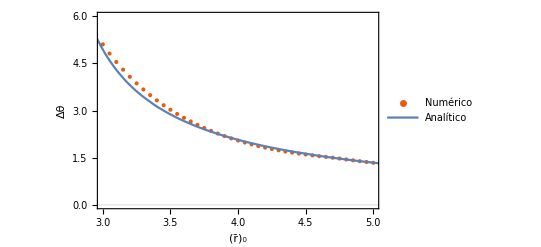

```mathematica
Show[{ListPlot[{Datos},PlotTheme->{"Scientific"},BaseStyle->14, FrameLabel->{"(r̄)_0","Δθ"},ImageSize->400,PlotRange->All,PlotLegends->Placed[{"Numérico"},Automatic]],Plot[Analit[x],{x,radio95,rMax+2},PlotRange->All,PlotLegends->Placed[{"Analítico"},Automatic]]},
PlotRange->{{3,5},{0,6}}
]
```

```mathematica
num=Interpolation[Datos]
```

InterpolatingFunction[…]

```mathematica
Dif[r_]:=1-num[r]/Analit[r];
```

```mathematica
Plot[Dif[x],{x,radio95-2,rMax+10},PlotRange->All,PlotLegends->Placed[{"Black Hole"},Automatic],PlotTheme->"Scientific"]
```

Usando que b=√(r_0^2/NN[r_0]^2) notar que b si tiene unidades de distancia, por ende b=1/m √(((r̄)_0)^2/NN[r_0]^2)=1/m b̄

```mathematica
With[{NN=s[[1]]},
parb[r0_]:=N@(r0/NN[r0])];

Analparb[r0_]:=√(r0^3/(r0-2Masa));
```

```mathematica
Datos2={} (* la integral es integrando hasta una r0 sucesivamente y se guarda en Datos*);

For[r0=radio95,r0<rMax+2,r0+=0.05,
alpha=ang[r0];
paramb=parb[r0];
AppendTo[Datos2,{paramb,alpha}]
]
```

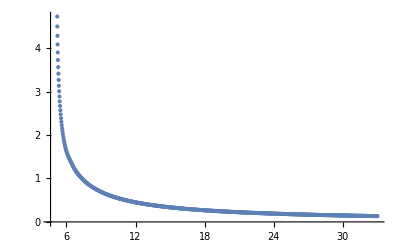

```mathematica
ListPlot[Datos2,PlotRange->All]
```

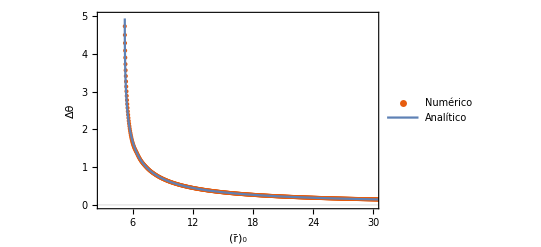

```mathematica
Show[{ListPlot[{Datos2},PlotTheme->{"Scientific"},BaseStyle->14, FrameLabel->{"(r̄)_0","Δθ"},ImageSize->400,PlotRange->All,PlotLegends->Placed[{"Numérico"},Automatic]],ParametricPlot[{Analparb[x],Analit[x]},{x,radio95,rMax+2},PlotRange->All,PlotLegends->Placed[{"Analítico"},Automatic]]},
PlotRange->{{3,30},{0,5}}
]
```

### beyond Horndeski

```mathematica
Quit[];
```

```mathematica
ClearAll[NN,gg,z,r0,nlm,VG,sigma,delta,rh0,PotAnalit,Analit,radio95,Nfun,gfun,r]
```

```mathematica
(*Definiendo el potencial*)

With[{NN=NN/.s[[1,1]],gg=gg/.s[[1,2]]},
(*V[z_,r0_]:=z^2 1/gg[r0/z]-NN[r0]/(gg[r0/z]NN[r0/z])+NN[r0];*) (* diverge pq interpola fuera del valor *)
VG[z_,r0_]:=Piecewise[{{z^2 1/gg[r0/z]^2-NN[r0]^2/(gg[r0/z]^2 NN[r0/z]^2)+NN[r0]^2,r0/z<=rMax},{z^2-(2Masa)/r0 z^3,r0/z>rMax}}];
]

(* *)
vs[r0_]:=Module[{r0v=r0},
(* Generating data *)
data={};
Do[AppendTo[data,{z,VG[z,r0v]}],{z,10^-5,1,0.001}];

(* Fit v1,....,v6 *)
nlm=NonlinearModelFit[data,v1 x+v2 x^2+v3 x^3+v4 x^4+v5 x^5+v6 x^6,{v1,v2,v3,v4,v5,v6},x];

(* checking *)
(*
Print[Grid[{{
ListPlot[{nlm["FitResiduals"]},BaseStyle->14, FrameLabel->{"points","Residuals"},PlotRange->All,PlotTheme->{"Scientific"},ImageSize->400,Filling->Axis],

Show[{ListPlot[{data},PlotTheme->{"Scientific"},BaseStyle->14, FrameLabel->{"z","V(z)"},ImageSize->400,PlotRange->All],Plot[nlm[x],{x,0,1}],Plot[PotAnalit[x,r0],{x,0,1}]},PlotLegends->Placed[{"data","Fit"},Automatic]]
}},Alignment->{{Left,Right}}]
];
*)

Return[nlm["BestFitParameters"]]
]

(*Definiendo la función rho*)
rho[r0_]:=Module[{r0v=r0},
sigma[n_]:=√π Gamma[n/2+1/2]/Gamma[n/2];
v=vs[r0v];
(* se definió desde n=1 to 6*)
rh0=Sum[v[[n,2]]sigma[n]z^n,{n,1,6}];

Return[rh0]
]

(* Definiendo el angulo *)
ang[r0_]:=Module[{r0v=r0},
delta=π(√(π/(2(rho[r0v]/.z-> 1)))-1);
Return[delta]
]
```

```mathematica
PotAnalit[z_,r0_]:=z^2-(2Masa)/r0 z^3;
Analit[r0_]:=π(√(1/(1-(8Masa)/(π r0)))-1); (* paper*)
```

Calculando ángulo vs

```mathematica
radio95=rad[[2]]
```

13.181

```mathematica
Masa
```

0.522599

```mathematica
Datos={} (* la integral es integrando hasta una r0 sucesivamente y se guarda en Datos*);

For[r0=radio95-2,r0<rMax+10,r0+=0.05,
alpha=ang[r0];
AppendTo[Datos,{r0,alpha}]
]
```

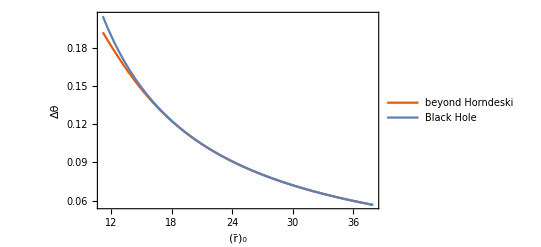

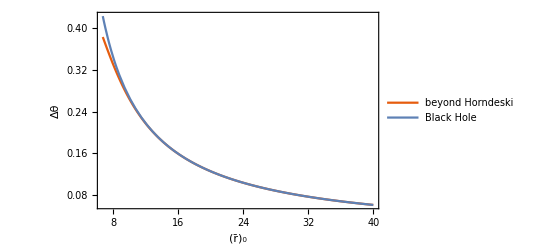

```mathematica
Show[{ListPlot[{Datos},PlotTheme->{"Scientific"},BaseStyle->14, FrameLabel->{"(r̄)_0","Δθ"},ImageSize->400,PlotRange->All,PlotLegends->Placed[{"beyond Horndeski"},Automatic],Joined->True],Plot[Analit[x],{x,radio95-2,rMax+10},PlotRange->All,PlotLegends->Placed[{"Black Hole"},Automatic]]},
PlotRange->All(*{{12,rMax+10},{0.05,0.23}}*)
]
```

```mathematica
Export["Lensing_beyond_X_0015.dat",Datos]
```

Lensing_beyond_X_0015.dat

```mathematica
"Lensing_beyond_X_0015.dat"
```

```mathematica
num=Interpolation[Datos]
```

InterpolatingFunction[…]

```mathematica
Dif[r_]:=1-num[r]/Analit[r];
```

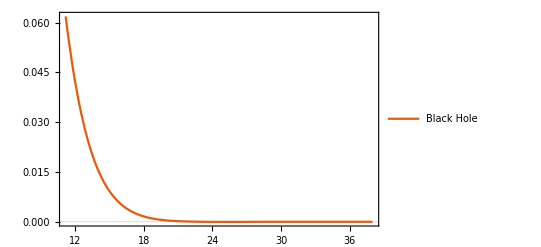

```mathematica
Plot[Dif[x],{x,radio95-2,rMax+10},PlotRange->All,PlotLegends->Placed[{"Black Hole"},Automatic],PlotTheme->"Scientific"]
```

```mathematica
Diff={};
Do[AppendTo[Diff,{r,Dif[r]}],{r,radio95-2,rMax+10,0.05}]
```

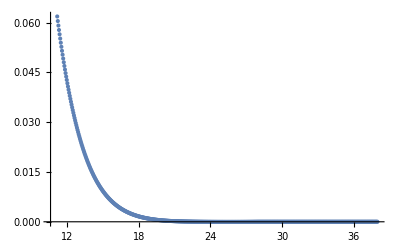

```mathematica
ListPlot[Diff,PlotRange->All]
```

```mathematica
Export["Dif_Lensing_beyond_X_0015.dat",Diff]
```

Dif_Lensing_beyond_X_0015.dat

Usando que b=√(r_0^2/NN[r_0]^2) notar que b si tiene unidades de distancia, por ende b=1/m √(((r̄)_0)^2/NN[r_0]^2)=1/m b̄

```mathematica
With[{NN=NN/.s[[1,1]]},
parb[r0_]:=Piecewise[{{N@(r0/NN[r0]),r0<=rMax},{√(r0^3/(r0-2Masa)),r0>rMax}}]
];
Analparb[r0_]:=√(r0^3/(r0-2Masa));(* black Hole *)
```

```mathematica
Datos2={} (* la integral es integrando hasta una r0 sucesivamente y se guarda en Datos*);

For[r0=radio95,r0<rMax+10,r0+=0.05,
alpha=ang[r0];
paramb=parb[r0];
AppendTo[Datos2,{paramb,alpha}]
]
```

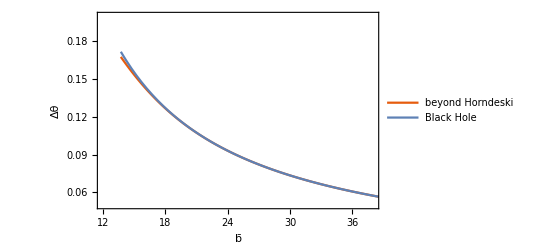

```mathematica
Show[{ListPlot[{Datos2},PlotTheme->{"Scientific"},BaseStyle->14, FrameLabel->{"b̄","Δθ"},ImageSize->400,PlotRange->All,PlotLegends->Placed[{"beyond Horndeski"},Automatic],Joined->True],ParametricPlot[{Analparb[x],Analit[x]},{x,radio95,rMax+10},PlotRange->All,PlotLegends->Placed[{"Black Hole"},Automatic]]},
PlotRange->{{12,rMax+10},{0.05,0.2}}
]
```

## Lente fuerte

En unidades del paper A=NN, B=gg

α=2|∫_r0^∞ √(B/R)ⅆr/r|-π

R=(r^2 A_m)/(r_m^2 A)-1

```mathematica
z=r0/r
```

```mathematica
gg[r] √(NN[r]^2/(NN[r0]^2-z^2 NN[r]^2))dz
```

```mathematica
ClearAll[rm,r0,alpha] 
(* Defining R for every region *)
funcR[r_]:=(r^2 NN[r0]^2)/(r0^2 NN[r]^2)-1;   (* B. S.*)
funcRS[r_]:=(r^2(1-(2Masa)/r0))/(r0^2(1-(2Masa)/r))-1;    (* Sch.*)

(* Definiendo el integrando *)
With[{NN=NN/.s[[1,1]],gg=gg/.s[[1,2]]},
integrando[r_]:=Piecewise[{{Sqrt[gg[r]^2/funcR[r]] 1/r,r<=rMax},{Sqrt[(1-(2Masa)/r)^-1/funcRS[r]] 1/r,r>rMax}}] (* Numerica para r ≤ rMax, Sch para r>rMax *)
];

(* definición simplificada del integrando*)
With[{NN=NN/.s[[1,1]],gg=gg/.s[[1,2]]},
integrandoS[r_]:=Piecewise[{{gg[r]/r √((NN[r]^2 r0^2)/(r^2 NN[r0]^2-r0^2 NN[r]^2)),r<=rMax},{Sqrt[(1-(2Masa)/r)^-1/funcRS[r]] 1/r,r>rMax}}] (* Numerica para r ≤ rMax, Sch para r>rMax *)
];

(* parámetro de impacto  *)
With[{NN=NN/.s[[1,1]]},
b[r_]:=√(r0^2/NN[r0]^2)
];
bS[r_]:=√(r0^2/(1-(2Masa)/r0));

(* definición simplificada del integrando*)
integrandoSch[r_]:=Sqrt[(1-(2Masa)/r)^-1/funcRS[r]] 1/r ;
```

Notar que para el caso de la estrella de bosones, siempre que r0>rm es positiva la raíz, ahora para la zona fuera de la estrella de bosones, Sch. para que la raíz sea positiva se tiene que tener lo usual, que

```mathematica
Reduce[{(1-(2Mas)/rml)>0,Mas>0,rml>0},rml]//Simplify
```

Mas>0&&rml>2 Mas

por tanto:    rml > 2 Masa del objeto y r0 debe ser mayor 2 Masa

### Checking

Checking the results if we solve the integration for part

```mathematica
ClearAll[rm,r0] (* clear the values evaluate in the function funcR, funcRS, integrando *)
rm=2.01 Masa;
r0=2.02 Masa;
part1=NIntegrate[Evaluate[Sqrt[gg[r]^2/funcR[r]] 1/r/.s],{r,r0,rMax}][[1]]
part2=NIntegrate[Sqrt[(1-(2Masa)/r)^-1/funcRS[r]] 1/r,{r,rMax,Infinity}]
2(part1+part2)

2NIntegrate[Evaluate[integrando[r]/.s],{r,r0,Infinity}]
2NIntegrate[Evaluate[integrandoS[r]/.s],{r,r0,Infinity}]
```

1.62086

0.758585

4.75888

{4.75888}

{4.75888}

Checking two, taking rm and r0 in the region where the metric term gg and NN are equivalent to sch. term. For this case, is the same take gg, NN or sch. term

```mathematica
ClearAll[rm,r0] (* clear the values evaluate in the function funcR, funcRS, integrando *)
```

```mathematica
rm=rMax-15(*(3+√(9+32γ))/4/.γ-> -1/4*);
r0=rMax-1;
```

```mathematica
NumberForm[2NIntegrate[Evaluate[integrando[r]/.s],{r,r0,Infinity}][[1]],{22,20}]
NumberForm[2NIntegrate[Sqrt[(1-(2Masa)/r)^-1/funcRS[r]] 1/r,{r,r0,Infinity}],{22,20}]
```

3.29588297379726600000

3.29590572509786700000

### Gráficos

Sch  con la masa de la estrella -- r95 --- 2 veces r95

```mathematica
ClearAll[r0,alpha,alphaS]
```

```mathematica
rMax
```

20.

```mathematica
rS=rMax-10;
Datos={} (* la integral es integrando hasta una r0 sucesivamente y se guarda en Datos*);
Datos2={} ;
Datos3={} ;
Datos4={} ;
For[r0=rS,r0<2*rMax,r0+=0.05,
alpha=2NIntegrate[Evaluate[integrando[r]/.s],{r,r0,Infinity}]-π;
(*alphaS=2NIntegrate[integrandoSch[r],{r,r0,Infinity}]-π;*)
AppendTo[Datos,{r0,alpha[[1]]}];
AppendTo[Datos2,{Evaluate[b[r0]/.s][[1]],alpha[[1]]}]
(*AppendTo[Datos3,{r0,alphaS[[1]]}];
AppendTo[Datos4,{bS[r0],alpha[[1]]}]*)
]
```

InterpolatingFunction::dmval: Input value {20.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

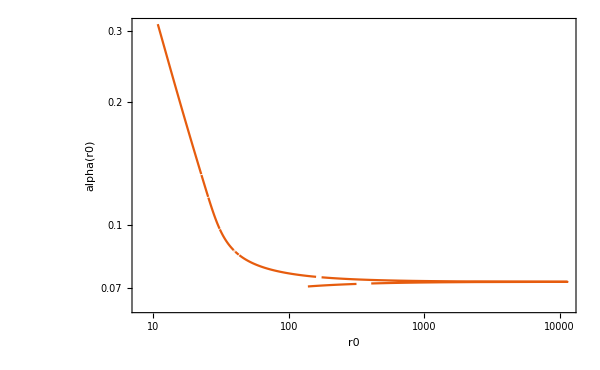

```mathematica
ListLogLogPlot[{Datos2},PlotTheme->"Scientific",ImageSize->600,BaseStyle->14, FrameLabel->{"r0","alpha(r0)"},PlotRange->All,Joined->True]
```

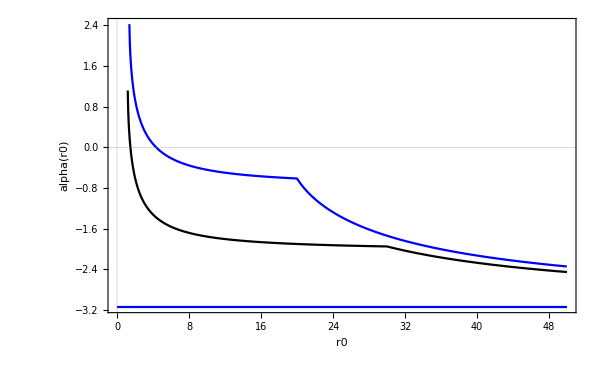

```mathematica
ListPlot[{Datos,DatosGR,{{0,-π},{50,-π}}},PlotTheme->"Scientific",ImageSize->600,BaseStyle->14, FrameLabel->{"r0","alpha(r0)"},PlotStyle->{Blue,Black},Joined->True]
```

```mathematica
DatosGR={{1.1956893351543199,1.1193258780613116},{1.24568933515432,0.7089315947997941},{1.29568933515432,0.49160078179829547},{1.34568933515432,0.3299388367789007},{1.39568933515432,0.198840978590491},{1.44568933515432,0.08789315934378017},{1.4956893351543201,-0.008472633088048909},{1.5456893351543202,-0.0936673245821611},{1.5956893351543202,-0.16996810258746908},{1.6456893351543203,-0.23898838396377364},{1.6956893351543203,-0.30192218017643313},{1.7456893351543203,-0.3596829998170197},{1.7956893351543204,-0.4129883004843462},{1.8456893351543204,-0.4624136171100002},{1.8956893351543205,-0.5084287635907456},{1.9456893351543205,-0.5514229051825668},{1.9956893351543206,-0.5917224397243084},{2.0456893351543206,-0.6296040717324782},{2.0956893351543204,-0.6653045772842372},{2.1456893351543203,-0.699028234295076},{2.19568933515432,-0.7309525688453249},{2.24568933515432,-0.7612328631883072},{2.2956893351543197,-0.7900057376390626},{2.3456893351543195,-0.8173920294022965},{2.3956893351543194,-0.8434991300338641},{2.445689335154319,-0.8684229007840916},{2.495689335154319,-0.8922492558894337},{2.545689335154319,-0.9150554809102935},{2.5956893351543187,-0.9369113382568033},{2.6456893351543185,-0.9578800008864103},{2.6956893351543183,-0.9780188446483988},{2.745689335154318,-0.9973801250205367},{2.795689335154318,-1.0160115582625506},{2.8456893351543178,-1.033956821932117},{2.8956893351543176,-1.0512559889741944},{2.9456893351543174,-1.0679459052414657},{2.9956893351543172,-1.0840605186751038},{3.045689335154317,-1.099631168528087},{3.095689335154317,-1.1146868392410196},{3.1456893351543167,-1.1292543843616114},{3.1956893351543165,-1.1433587253210684},{3.2456893351543163,-1.1570230271616404},{3.295689335154316,-1.1702688553015752},{3.345689335154316,-1.1831163156547564},{3.395689335154316,-1.195584179348135},{3.4456893351543156,-1.2076899951995574},{3.4956893351543155,-1.2194501905774204},{3.5456893351543153,-1.2308801619360954},{3.595689335154315,-1.2419943571673928},{3.645689335154315,-1.252806349535171},{3.6956893351543147,-1.2633289047597531},{3.7456893351543146,-1.273574042291376},{3.7956893351543144,-1.2835530904366854},{3.845689335154314,-1.293276736974731},{3.895689335154314,-1.302755075336684},{3.945689335154314,-1.3119976464057503},{3.9956893351543137,-1.321013477269038},{4.0456893351543135,-1.3298111164238178},{4.095689335154313,-1.3383986659984586},{4.145689335154313,-1.3467838117367956},{4.195689335154313,-1.3549738501632584},{4.245689335154313,-1.3629757137914338},{4.295689335154313,-1.37079599450109},{4.345689335154312,-1.3784409647808293},{4.395689335154312,-1.3859165976815109},{4.445689335154312,-1.3932285851649953},{4.495689335154312,-1.4003823549547456},{4.545689335154312,-1.4073830864454155},{4.5956893351543116,-1.4142357252281261},{4.645689335154311,-1.4209449966338257},{4.695689335154311,-1.4275154184719447},{4.745689335154311,-1.4339513126566708},{4.795689335154311,-1.4402568162016367},{4.845689335154311,-1.446435891456539},{4.8956893351543105,-1.4524923355326953},{4.94568933515431,-1.4584297892784663},{4.99568933515431,-1.464251745554947},{5.04568933515431,-1.469961556969618},{5.09568933515431,-1.475562443220292},{5.14568933515431,-1.4810574978485902},{5.195689335154309,-1.4864496946416637},{5.245689335154309,-1.4917418936531814},{5.295689335154309,-1.4969368467778943},{5.345689335154309,-1.5020372030751763},{5.395689335154309,-1.5070455137282868},{5.4456893351543085,-1.5119642366957513},{5.495689335154308,-1.5167957411448332},{5.545689335154308,-1.52154231157045},{5.595689335154308,-1.5262061517057415},{5.645689335154308,-1.5307893882200307},{5.695689335154308,-1.5352940741748253},{5.7456893351543075,-1.539722192323791},{5.795689335154307,-1.5440756582105895},{5.845689335154307,-1.5483563230959616},{5.895689335154307,-1.5525659767452908},{5.945689335154307,-1.55670635004464},{5.995689335154307,-1.5607791174946795},{6.045689335154306,-1.5647858995695265},{6.095689335154306,-1.5687282649466225},{6.145689335154306,-1.5726077326368872},{6.195689335154306,-1.5764257739904144},{6.245689335154306,-1.5801838146122664},{6.2956893351543055,-1.5838832361827269},{6.345689335154305,-1.5875253781770913},{6.395689335154305,-1.5911115395185527},{6.445689335154305,-1.5946429801364355},{6.495689335154305,-1.5981209224544606},{6.545689335154305,-1.6015465528178754},{6.5956893351543044,-1.604921022834855},{6.645689335154304,-1.608245450673127},{6.695689335154304,-1.6115209222915015},{6.745689335154304,-1.614748492605163},{6.795689335154304,-1.6179291866183818},{6.845689335154304,-1.621064000488491},{6.895689335154303,-1.6241539025482004},{6.945689335154303,-1.6271998342939664},{6.995689335154303,-1.6302027113106417},{7.045689335154303,-1.6331634241741044},{7.095689335154303,-1.6360828393118636},{7.1456893351543025,-1.638961799814584},{7.195689335154302,-1.6418011262343697},{7.245689335154302,-1.6446016173340463},{7.295689335154302,-1.6473640508071488},{7.345689335154302,-1.6500891839820455},{7.395689335154302,-1.6527777544776598},{7.445689335154301,-1.6554304808467801},{7.495689335154301,-1.6580480631946908},{7.545689335154301,-1.6606311837588477},{7.595689335154301,-1.6631805074845083},{7.645689335154301,-1.6656966825672428},{7.6956893351543005,-1.668180340971428},{7.7456893351543,-1.6706320989435741},{7.7956893351543,-1.673052557489663},{7.8456893351543,-1.6754423028428995},{7.8956893351543,-1.6778019069189538},{7.9456893351543,-1.6801319277399132},{7.9956893351542995,-1.6824329098572028},{8.0456893351543,-1.684705384753785},{8.095689335154301,-1.6869498712253037},{8.145689335154302,-1.6891668757655576},{8.195689335154302,-1.691356892923098},{8.245689335154303,-1.6935204056289073},{8.295689335154304,-1.6956578855400424},{8.345689335154304,-1.6977697933745768},{8.395689335154305,-1.6998565792341478},{8.445689335154306,-1.701918682900744},{8.495689335154307,-1.703956534105198},{8.545689335154307,-1.7059705528113995},{8.595689335154308,-1.7079611494982454},{8.645689335154309,-1.7099287254317965},{8.69568933515431,-1.7118736729245159},{8.74568933515431,-1.7137963755646046},{8.79568933515431,-1.7156972084456004},{8.845689335154312,-1.7175765384040962},{8.895689335154312,-1.7194347242502412},{8.945689335154313,-1.7212721169899021},{8.995689335154314,-1.7230890600272843},{9.045689335154314,-1.7248858893533012},{9.095689335154315,-1.7266629337448833},{9.145689335154316,-1.7284205149610692},{9.195689335154317,-1.7301589479326163},{9.245689335154317,-1.7318785409400301},{9.295689335154318,-1.7335795957732274},{9.345689335154319,-1.7352624078979404},{9.39568933515432,-1.7369272666231397},{9.44568933515432,-1.738574455263203},{9.49568933515432,-1.7402042512934228},{9.545689335154321,-1.7418169264890242},{9.595689335154322,-1.743412747063334},{9.645689335154323,-1.7449919738110746},{9.695689335154324,-1.746554862247565},{9.745689335154324,-1.7481016627434358},{9.795689335154325,-1.7496326206488528},{9.845689335154326,-1.7511479764086104},{9.895689335154326,-1.752647965684213},{9.945689335154327,-1.7541328194738521},{9.995689335154328,-1.755602764228708},{10.045689335154329,-1.7570580219638159},{10.09568933515433,-1.758498810357369},{10.14568933515433,-1.7599253428532369},{10.19568933515433,-1.7613378287647752},{10.245689335154331,-1.7627364733754392},{10.295689335154332,-1.7641214780361447},{10.345689335154333,-1.765493040254242},{10.395689335154334,-1.766851353779094},{10.445689335154334,-1.768196608691916},{10.495689335154335,-1.7695289914931074},{10.545689335154336,-1.7708486851870497},{10.595689335154336,-1.7721558693623347},{10.645689335154337,-1.7734507202648064},{10.695689335154338,-1.7747334108744983},{10.745689335154339,-1.7760041109818125},{10.79568933515434,-1.7772629872613788},{10.84568933515434,-1.7785102033434326},{10.89568933515434,-1.7797459198787307},{10.945689335154341,-1.7809702946033656},{10.995689335154342,-1.7821834824054945},{11.045689335154343,-1.7833856353898532},{11.095689335154344,-1.784576902940488},{11.145689335154344,-1.7857574317797176},{11.195689335154345,-1.786927366023157},{11.245689335154346,-1.7880868472376936},{11.295689335154346,-1.7892360144980932},{11.345689335154347,-1.790375004441994},{11.395689335154348,-1.7915039513229507},{11.445689335154348,-1.7926229870589894},{11.49568933515435,-1.7937322412821133},{11.54568933515435,-1.7948318413882074},{11.59568933515435,-1.7959219125853503},{11.645689335154351,-1.7970025779408259},{11.695689335154352,-1.7980739584251975},{11.745689335154353,-1.7991361729545177},{11.795689335154353,-1.8001893384342176},{11.845689335154354,-1.8012335698016995},{11.895689335154355,-1.8022689800678062},{11.945689335154356,-1.8032956803567268},{11.995689335154356,-1.8043137799429636},{12.045689335154357,-1.805323386289425},{12.095689335154358,-1.8063246050851651},{12.145689335154358,-1.8073175402820096},{12.19568933515436,-1.8083022941302023},{12.24568933515436,-1.8092789672118208},{12.29568933515436,-1.8102476584735046},{12.345689335154361,-1.8112084652599525},{12.395689335154362,-1.8121614833463608},{12.445689335154363,-1.8131068069700578},{12.495689335154363,-1.8140445288608884},{12.545689335154364,-1.8149747402698084},{12.595689335154365,-1.8158975309983219},{12.645689335154366,-1.816812989427333},{12.695689335154366,-1.8177212025452327},{12.745689335154367,-1.818622255975228},{12.795689335154368,-1.8195162340010658},{12.845689335154368,-1.820403219592614},{12.895689335154369,-1.8212832944316126},{12.94568933515437,-1.8221565389366572},{12.99568933515437,-1.8230230322875953},{13.045689335154371,-1.8238828524489352},{13.095689335154372,-1.8247360761922389},{13.145689335154373,-1.825582779118995},{13.195689335154373,-1.8264230356829243},{13.245689335154374,-1.8272569192117363},{13.295689335154375,-1.828084501928302},{13.345689335154375,-1.8289058549707033},{13.395689335154376,-1.829721048412352},{13.445689335154377,-1.8305301512819794},{13.495689335154378,-1.831333231583077},{13.545689335154378,-1.8321303563128981},{13.595689335154379,-1.832921591480694},{13.64568933515438,-1.8337070021254038},{13.69568933515438,-1.834486652333553},{13.745689335154381,-1.8352606052566705},{13.795689335154382,-1.8360289231283144},{13.845689335154383,-1.8367916672806315},{13.895689335154383,-1.8375488981601706},{13.945689335154384,-1.8383006753437816},{13.995689335154385,-1.8390470575542825},{14.045689335154385,-1.8397881026757315},{14.095689335154386,-1.8405238677683653},{14.145689335154387,-1.8412544090829615},{14.195689335154388,-1.8419797820749197},{14.245689335154388,-1.8427000414183632},{14.295689335154389,-1.8434152410198732},{14.34568933515439,-1.8441254340319322},{14.39568933515439,-1.8448306728659962},{14.445689335154391,-1.8455310092050912},{14.495689335154392,-1.8462264940164483},{14.545689335154393,-1.8469171775638955},{14.595689335154393,-1.8476031094199645},{14.645689335154394,-1.8482843384777365},{14.695689335154395,-1.8489609129622635},{14.745689335154395,-1.8496328804418485},{14.795689335154396,-1.850300287839242},{14.845689335154397,-1.8509631814425727},{14.895689335154398,-1.8516216069160483},{14.945689335154398,-1.852275609310373},{14.995689335154399,-1.8529252330728556},{15.0456893351544,-1.8535705220575185},{15.0956893351544,-1.8542115195349806},{15.145689335154401,-1.8548482682021383},{15.195689335154402,-1.8554808101916342},{15.245689335154402,-1.8561091870810262},{15.295689335154403,-1.8567334399018711},{15.345689335154404,-1.8573536091486886},{15.395689335154405,-1.8579697347877282},{15.445689335154405,-1.8585818562655598},{15.495689335154406,-1.8591900125174425},{15.545689335154407,-1.8597942419754978},{15.595689335154407,-1.8603945825768453},{15.645689335154408,-1.8609910717715525},{15.695689335154409,-1.861583746530434},{15.74568933515441,-1.8621726433526775},{15.79568933515441,-1.862757798273241},{15.845689335154411,-1.863339246870213},{15.895689335154412,-1.8639170242720482},{15.945689335154412,-1.8644911651646563},{15.995689335154413,-1.8650617037983506},{16.045689335154414,-1.8656286739946695},{16.095689335154415,-1.8661921091530695},{16.145689335154415,-1.8667520422574926},{16.195689335154416,-1.8673085058828107},{16.245689335154417,-1.8678615322011534},{16.295689335154417,-1.8684111529880112},{16.345689335154418,-1.8689573996280822},{16.39568933515442,-1.8695003031214887},{16.44568933515442,-1.870039894089714},{16.49568933515442,-1.8705762027813702},{16.54568933515442,-1.871109259077857},{16.59568933515442,-1.8716390924989232},{16.645689335154422,-1.8721657322081207},{16.695689335154423,-1.872689207018166},{16.745689335154424,-1.873209545396199},{16.795689335154425,-1.8737267754687572},{16.845689335154425,-1.874240925026681},{16.895689335154426,-1.874752021530382},{16.945689335154427,-1.8752600921147757},{16.995689335154427,-1.875765163594091},{17.045689335154428,-1.8762672624665968},{17.09568933515443,-1.876766414919242},{17.14568933515443,-1.877262646832218},{17.19568933515443,-1.8777559837834374},{17.24568933515443,-1.8782464510529304},{17.29568933515443,-1.8787340736270202},{17.345689335154432,-1.8792188762025512},{17.395689335154433,-1.879700883191199},{17.445689335154434,-1.8801801187235818},{17.495689335154434,-1.8806566066532944},{17.545689335154435,-1.8811303705608733},{17.595689335154436,-1.8816014337576958},{17.645689335154437,-1.882069819289808},{17.695689335154437,-1.8825355499416916},{17.745689335154438,-1.8829986482399486},{17.79568933515444,-1.883459136456803},{17.84568933515444,-1.8839170366137301},{17.89568933515444,-1.8843723704850603},{17.94568933515444,-1.8848251596014354},{17.99568933515444,-1.8852754252532082},{18.045689335154442,-1.88572318849379},{18.095689335154443,-1.886168470142933},{18.145689335154444,-1.8866112907899693},{18.195689335154444,-1.8870516707969855},{18.245689335154445,-1.8874896303019395},{18.295689335154446,-1.8879251892216766},{18.345689335154447,-1.888358367254996},{18.395689335154447,-1.8887891838856432},{18.445689335154448,-1.8892176583852405},{18.49568933515445,-1.8896438098161648},{18.54568933515445,-1.89006765703438},{18.59568933515445,-1.8904892186922244},{18.64568933515445,-1.8909085132411532},{18.69568933515445,-1.8913255589344344},{18.745689335154452,-1.8917403738297849},{18.795689335154453,-1.892152975791951},{18.845689335154454,-1.8925633824953247},{18.895689335154454,-1.892971611426478},{18.945689335154455,-1.8933776798866542},{18.995689335154456,-1.8937816049942136},{19.045689335154457,-1.8941834036870477},{19.095689335154457,-1.8945830927249485},{19.145689335154458,-1.894980688691946},{19.19568933515446,-1.8953762079986043},{19.24568933515446,-1.8957696668842625},{19.29568933515446,-1.896161081419255},{19.34568933515446,-1.8965504675071325},{19.39568933515446,-1.8969378408868232},{19.445689335154462,-1.8973232171347592},{19.495689335154463,-1.8977066116669663},{19.545689335154464,-1.898088039741125},{19.595689335154464,-1.8984675164585982},{19.645689335154465,-1.8988450567664295},{19.695689335154466,-1.8992206754593055},{19.745689335154466,-1.899594387181474},{19.795689335154467,-1.899966206428656},{19.845689335154468,-1.9003361475499432},{19.89568933515447,-1.9007042247496488},{19.94568933515447,-1.9010704520891273},{19.99568933515447,-1.9014348434885702},{20.04568933515447,-1.9017974127287727},{20.09568933515447,-1.9021581734528752},{20.145689335154472,-1.9025171391680766},{20.195689335154473,-1.9028743232473215},{20.245689335154474,-1.9032297389309543},{20.295689335154474,-1.9035833993283648},{20.345689335154475,-1.9039353174196152},{20.395689335154476,-1.9042855060570258},{20.445689335154476,-1.904633977966748},{20.495689335154477,-1.9049807457503047},{20.545689335154478,-1.9053258218861147},{20.59568933515448,-1.905669218730992},{20.64568933515448,-1.9060109485216237},{20.69568933515448,-1.9063510233760228},{20.74568933515448,-1.9066894552949636},{20.79568933515448,-1.9070262561633995},{20.845689335154482,-1.9073614377518617},{20.895689335154483,-1.9076950117178315},{20.945689335154484,-1.9080269896070954},{20.995689335154484,-1.9083573828550793},{21.045689335154485,-1.908686202788163},{21.095689335154486,-1.9090134606249798},{21.145689335154486,-1.9093391674776918},{21.195689335154487,-1.9096633343532505},{21.245689335154488,-1.9099859721546406},{21.29568933515449,-1.9103070916821068},{21.34568933515449,-1.9106267036343634},{21.39568933515449,-1.9109448186097842},{21.44568933515449,-1.9112614471075746},{21.49568933515449,-1.9115765995289324},{21.545689335154492,-1.9118902861781848},{21.595689335154493,-1.9122025172639163},{21.645689335154493,-1.9125133029000776},{21.695689335154494,-1.9128226531070789},{21.745689335154495,-1.9131305778128693},{21.795689335154496,-1.9134370868540072},{21.845689335154496,-1.913742189976706},{21.895689335154497,-1.9140458968378713},{21.945689335154498,-1.9143482170061201},{21.9956893351545,-1.914649159962789},{22.0456893351545,-1.9149487351029268},{22.0956893351545,-1.9152469517362722},{22.1456893351545,-1.915543819088223},{22.1956893351545,-1.915839346300786},{22.245689335154502,-1.916133542433521},{22.295689335154503,-1.916426416464469},{22.345689335154503,-1.9167179772910687},{22.395689335154504,-1.9170082337310563},{22.445689335154505,-1.9172971945233592},{22.495689335154506,-1.9175848683289716},{22.545689335154506,-1.9178712637318238},{22.595689335154507,-1.9181563892396363},{22.645689335154508,-1.9184402532847638},{22.69568933515451,-1.9187228642250274},{22.74568933515451,-1.9190042303445414},{22.79568933515451,-1.9192843598545215},{22.84568933515451,-1.919563260894086},{22.89568933515451,-1.9198409415310458},{22.945689335154512,-1.920117409762684},{22.995689335154513,-1.920392673516524},{23.045689335154513,-1.9206667406510887},{23.095689335154514,-1.92093961895665},{23.145689335154515,-1.9212113161559694},{23.195689335154515,-1.921481839905026},{23.245689335154516,-1.9217511977937414},{23.295689335154517,-1.9220193973466881},{23.345689335154518,-1.9222864460237936},{23.39568933515452,-1.9225523512210314},{23.44568933515452,-1.9228171202711062},{23.49568933515452,-1.9230807604441273},{23.54568933515452,-1.9233432789482774},{23.59568933515452,-1.9236046829304696},{23.645689335154522,-1.9238649794769964},{23.695689335154523,-1.9241241756141751},{23.745689335154523,-1.924382278308979},{23.795689335154524,-1.9246392944696642},{23.845689335154525,-1.9248952309463858},{23.895689335154525,-1.9251500945318085},{23.945689335154526,-1.9254038919617078},{23.995689335154527,-1.925656629915565},{24.045689335154528,-1.925908315017153},{24.09568933515453,-1.9261589538351171},{24.14568933515453,-1.9264085528835473},{24.19568933515453,-1.9266571186225456},{24.24568933515453,-1.9269046574587843},{24.29568933515453,-1.9271511757460549},{24.345689335154532,-1.927396679785816},{24.395689335154533,-1.9276411758277296},{24.445689335154533,-1.9278846700701915},{24.495689335154534,-1.9281271686608568},{24.545689335154535,-1.9283686776971583},{24.595689335154535,-1.928609203226817},{24.645689335154536,-1.928848751248351},{24.695689335154537,-1.929087327711573},{24.745689335154538,-1.9293249385180857},{24.795689335154538,-1.9295615895217688},{24.84568933515454,-1.9297972865292592},{24.89568933515454,-1.9300320353004286},{24.94568933515454,-1.930265841548851},{24.99568933515454,-1.93049871094227},{25.04568933515454,-1.9307306491030545},{25.095689335154542,-1.930961661608654},{25.145689335154543,-1.9311917539920462},{25.195689335154544,-1.9314209317421804},{25.245689335154545,-1.9316492003044146},{25.295689335154545,-1.9318765650809464},{25.345689335154546,-1.9321030314312422},{25.395689335154547,-1.9323286046724553},{25.445689335154547,-1.9325532900798472},{25.495689335154548,-1.9327770928871946},{25.54568933515455,-1.9330000182872005},{25.59568933515455,-1.9332220714318935},{25.64568933515455,-1.9334432574330291},{25.69568933515455,-1.9336635813624792},{25.74568933515455,-1.933883048252624},{25.795689335154552,-1.9341016630967327},{25.845689335154553,-1.9343194308493445},{25.895689335154554,-1.9345363564266438},{25.945689335154555,-1.9347524447068274},{25.995689335154555,-1.9349677005304753},{26.045689335154556,-1.9351821287009088},{26.095689335154557,-1.9353957339845511},{26.145689335154557,-1.9356085211112797},{26.195689335154558,-1.9358204947747764},{26.24568933515456,-1.9360316596328757},{26.29568933515456,-1.9362420203079047},{26.34568933515456,-1.9364515813870202},{26.39568933515456,-1.936660347422544},{26.44568933515456,-1.936868322932292},{26.495689335154562,-1.9370755123999017},{26.545689335154563,-1.9372819202751526},{26.595689335154564,-1.937487550974288},{26.645689335154565,-1.937692408880328},{26.695689335154565,-1.9378964983433833},{26.745689335154566,-1.938099823680962},{26.795689335154567,-1.9383023891782751},{26.845689335154567,-1.938504199088538},{26.895689335154568,-1.938705257633269},{26.94568933515457,-1.9389055690025825},{26.99568933515457,-1.9391051373554822},{27.04568933515457,-1.939303966820149},{27.09568933515457,-1.9395020614942289},{27.14568933515457,-1.939699425445113},{27.195689335154572,-1.9398960627102184},{27.245689335154573,-1.9400919772972598},{27.295689335154574,-1.9402871731845255},{27.345689335154574,-1.9404816543211445},{27.395689335154575,-1.940675424627356},{27.445689335154576,-1.9408684879947704},{27.495689335154577,-1.941060848286631},{27.545689335154577,-1.9412525093380726},{27.595689335154578,-1.941443474956377},{27.64568933515458,-1.941633748921224},{27.69568933515458,-1.9418233349849423},{27.74568933515458,-1.9420122368727561},{27.79568933515458,-1.9422004582830286},{27.84568933515458,-1.9423880028875056},{27.895689335154582,-1.9425748743315525},{27.945689335154583,-1.9427610762343934},{27.995689335154584,-1.9429466121893464},{28.045689335154584,-1.9431314857640531},{28.095689335154585,-1.9433157005007087},{28.145689335154586,-1.943499259916286},{28.195689335154587,-1.9436821675027613},{28.245689335154587,-1.9438644267273362},{28.295689335154588,-1.9440460410326557},{28.34568933515459,-1.9442270138370268},{28.39568933515459,-1.9444073485346318},{28.44568933515459,-1.944587048495741},{28.49568933515459,-1.9447661170669246},{28.54568933515459,-1.944944557571258},{28.595689335154592,-1.945122373308529},{28.645689335154593,-1.9452995675554425},{28.695689335154594,-1.9454761435658194},{28.745689335154594,-1.9456521045707995},{28.795689335154595,-1.945827453779036},{28.845689335154596,-1.9460021943768955},{28.895689335154596,-1.946176329528647},{28.945689335154597,-1.9463498623766555},{28.995689335154598,-1.9465227960415694},{29.0456893351546,-1.9466951336225091},{29.0956893351546,-1.9468668781972513},{29.1456893351546,-1.9470380328224137},{29.1956893351546,-1.9472086005336346},{29.2456893351546,-1.947378584345755},{29.295689335154602,-1.9475479872529942},{29.345689335154603,-1.9477168122291273},{29.395689335154604,-1.947885062227659},{29.445689335154604,-1.9480527401819954},{29.495689335154605,-1.9482198490056155},{29.545689335154606,-1.9483863915922406},{29.595689335154606,-1.948552370815999},{29.645689335154607,-1.9487177895315972},{29.695689335154608,-1.9488826505744785},{29.74568933515461,-1.9490469567609883},{29.79568933515461,-1.9492107108885337},{29.84568933515461,-1.949373915735741},{29.89568933515461,-1.9495365740626154},{29.94568933515461,-1.9496986886106944},{29.995689335154612,-1.9498602621032042},{30.045689335154613,-1.9519227440066647},{30.095689335154614,-1.9541559584206043},{30.145689335154614,-1.9563801997779229},{30.195689335154615,-1.9585955260932173},{30.245689335154616,-1.960801994845555},{30.295689335154616,-1.9629996629850526},{30.345689335154617,-1.9651885869393517},{30.395689335154618,-1.9673688226199917},{30.44568933515462,-1.969540425428688},{30.49568933515462,-1.9717034502635102},{30.54568933515462,-1.9738579515249683},{30.59568933515462,-1.9760039831220049},{30.64568933515462,-1.9781415984778938},{30.695689335154622,-1.9802708505360527},{30.745689335154623,-1.982391791765766},{30.795689335154623,-1.984504474167822},{30.845689335154624,-1.9866089492800638},{30.895689335154625,-1.9887052681828603},{30.945689335154626,-1.99079348150449},{30.995689335154626,-1.9928736394264532},{31.045689335154627,-1.9949457916886952},{31.095689335154628,-1.9970099875947618},{31.14568933515463,-1.9990662760168703},{31.19568933515463,-2.001114705400914},{31.24568933515463,-2.003155323771388},{31.29568933515463,-2.005188178736243},{31.34568933515463,-2.007213317491675},{31.395689335154632,-2.009230786826835},{31.445689335154633,-2.0112406331284802},{31.495689335154633,-2.0132429023855547},{31.545689335154634,-2.0152376401937007},{31.595689335154635,-2.0172248917597138},{31.645689335154636,-2.019204701905924},{31.695689335154636,-2.021177115074522},{31.745689335154637,-2.0231421753318255},{31.795689335154638,-2.0250999263724756},{31.84568933515464,-2.0270504115235846},{31.89568933515464,-2.0289936737488183},{31.94568933515464,-2.0309297556524264},{31.99568933515464,-2.0328586994832127},{32.04568933515464,-2.0347805471384506},{32.09568933515464,-2.0366953401677472},{32.145689335154636,-2.03860311977685},{32.19568933515463,-2.0405039268314042},{32.24568933515463,-2.0423978018606554},{32.29568933515463,-2.0442847850612207},{32.345689335154624,-2.0461649163002313},{32.39568933515462,-2.0480382351195736},{32.44568933515462,-2.04990478073894},{32.495689335154616,-2.051764592059399},{32.54568933515461,-2.053617707666811},{32.59568933515461,-2.0554641658351915},{32.64568933515461,-2.0573040045300317},{32.695689335154604,-2.0591372614115766},{32.7456893351546,-2.0609639738380565},{32.7956893351546,-2.062784178868876},{32.845689335154596,-2.064597913267761},{32.89568933515459,-2.066405213505866},{32.94568933515459,-2.068206115764837},{32.99568933515459,-2.070000655939836},{33.045689335154584,-2.0717888696425266},{33.09568933515458,-2.0735707922040163},{33.14568933515458,-2.0753464586777675},{33.195689335154576,-2.0771159038424636},{33.24568933515457,-2.078879162204843},{33.29568933515457,-2.0806362680024924},{33.34568933515457,-2.0823872552066067},{33.395689335154565,-2.084132157524715},{33.44568933515456,-2.0858710084033656},{33.49568933515456,-2.0876038410307824},{33.545689335154556,-2.089330688339485},{33.59568933515455,-2.091051583008875},{33.64568933515455,-2.0927665574677943},{33.69568933515455,-2.094475643897039},{33.745689335154545,-2.0961788742318577},{33.79568933515454,-2.0978762801644066},{33.84568933515454,-2.099567893146176},{33.895689335154536,-2.101253744390392},{33.94568933515453,-2.1029338648743776},{33.99568933515453,-2.104608285341898},{34.04568933515453,-2.1062770363054657},{34.095689335154525,-2.1079401480486206},{34.14568933515452,-2.1095976506281833},{34.19568933515452,-2.11124957387648},{34.245689335154516,-2.1128959474035387},{34.29568933515451,-2.114536800599259},{34.34568933515451,-2.116172162635558},{34.39568933515451,-2.1178020624684857},{34.445689335154505,-2.119426528840317},{34.4956893351545,-2.1210455902816205},{34.5456893351545,-2.122659275113295},{34.595689335154496,-2.124267611448592},{34.64568933515449,-2.125870627195104},{34.69568933515449,-2.127468350056736},{34.74568933515449,-2.129060807535647},{34.795689335154485,-2.1306480269341757},{34.84568933515448,-2.1322300353567383},{34.89568933515448,-2.1338068597117013},{34.945689335154476,-2.1353785267132404},{34.995689335154474,-2.1369450628831705},{35.04568933515447,-2.138506494552756},{35.09568933515447,-2.1400628478645007},{35.145689335154465,-2.1416141487739133},{35.19568933515446,-2.1431604230512624},{35.24568933515446,-2.1447016962832937},{35.29568933515446,-2.146237993874945},{35.345689335154454,-2.1477693410510286},{35.39568933515445,-2.149295762857901},{35.44568933515445,-2.150817284165111},{35.495689335154445,-2.1523339296670287},{35.54568933515444,-2.153845723884457},{35.59568933515444,-2.155352691166221},{35.64568933515444,-2.156854855690746},{35.695689335154434,-2.158352241467609},{35.74568933515443,-2.15984487233908},{35.79568933515443,-2.1613327719816424},{35.845689335154425,-2.1628159639074935},{35.89568933515442,-2.164294471466035},{35.94568933515442,-2.165768317845339},{35.99568933515442,-2.1672375260736034},{36.045689335154414,-2.168702119020588},{36.09568933515441,-2.1701621193990355},{36.14568933515441,-2.171617549766075},{36.195689335154405,-2.1730684325246106},{36.2456893351544,-2.1745147899246993},{36.2956893351544,-2.175956644064904},{36.3456893351544,-2.1773940168936403},{36.395689335154394,-2.1788269302105028},{36.44568933515439,-2.180255405667581},{36.49568933515439,-2.1816794647707574},{36.545689335154385,-2.183099128880992},{36.59568933515438,-2.1845144192155956},{36.64568933515438,-2.1859253568494843},{36.69568933515438,-2.1873319627164247},{36.745689335154374,-2.1887342576102635},{36.79568933515437,-2.190132262186143},{36.84568933515437,-2.1915259969617074},{36.895689335154366,-2.1929154823182877},{36.94568933515436,-2.1943007385020867},{36.99568933515436,-2.1956817856253377},{37.04568933515436,-2.1970586436674586},{37.095689335154354,-2.1984313324761944},{37.14568933515435,-2.199799871768742},{37.19568933515435,-2.201164281132869},{37.245689335154346,-2.202524580028013},{37.29568933515434,-2.20388078778638},{37.34568933515434,-2.20523292361402},{37.39568933515434,-2.2065810065918994},{37.445689335154334,-2.2079250556769576},{37.49568933515433,-2.2092650897031545},{37.54568933515433,-2.210601127382506},{37.595689335154326,-2.2119331873061094},{37.64568933515432,-2.2132612879451576},{37.69568933515432,-2.214585447651943},{37.74568933515432,-2.215905684660851},{37.795689335154314,-2.217222017089343},{37.84568933515431,-2.218534462938927},{37.89568933515431,-2.219843040096125},{37.945689335154306,-2.2211477663334227},{37.9956893351543,-2.222448659310211},{38.0456893351543,-2.2237457365737243},{38.0956893351543,-2.22503901555996},{38.145689335154294,-2.2263285135945936},{38.19568933515429,-2.227614247893886},{38.24568933515429,-2.228896235565576},{38.295689335154286,-2.23017449360977},{38.34568933515428,-2.2314490389198167},{38.39568933515428,-2.2327198882831785},{38.44568933515428,-2.233987058382291},{38.495689335154275,-2.235250565795413},{38.54568933515427,-2.2365104269974694},{38.59568933515427,-2.237766658360888},{38.645689335154266,-2.239019276156423},{38.69568933515426,-2.240268296553972},{38.74568933515426,-2.2415137356233896},{38.79568933515426,-2.242755609335284},{38.845689335154255,-2.2439939335618138},{38.89568933515425,-2.2452287240774726},{38.94568933515425,-2.2464599965598664},{38.995689335154246,-2.247687766590485},{39.04568933515424,-2.248912049655463},{39.09568933515424,-2.2501328611463367},{39.14568933515424,-2.25135021636079},{39.195689335154235,-2.2525641305033974},{39.24568933515423,-2.2537746186863528},{39.29568933515423,-2.2549816959301996},{39.345689335154226,-2.256185377164548},{39.39568933515422,-2.257385677228786},{39.44568933515422,-2.2585826108727876},{39.49568933515422,-2.2597761927576063},{39.545689335154215,-2.2609664374561698},{39.59568933515421,-2.262153359453965},{39.64568933515421,-2.263336973149713},{39.695689335154206,-2.264517292856045},{39.7456893351542,-2.2656943328001633},{39.7956893351542,-2.2668681071245045},{39.8456893351542,-2.268038629887388},{39.895689335154195,-2.269205915063665},{39.94568933515419,-2.270369976545358},{39.99568933515419,-2.271530828142295},{40.04568933515419,-2.272688483582736},{40.095689335154184,-2.273842956513998},{40.14568933515418,-2.2749942605030693},{40.19568933515418,-2.2761424090372198},{40.245689335154175,-2.277287415524609},{40.29568933515417,-2.278429293294879},{40.34568933515417,-2.2795680555997544},{40.39568933515417,-2.280703715613626},{40.445689335154164,-2.2818362864341344},{40.49568933515416,-2.2829657810827486},{40.54568933515416,-2.2840922125053345},{40.595689335154155,-2.2852155935727234},{40.64568933515415,-2.2863359370812724},{40.69568933515415,-2.2874532557534217},{40.74568933515415,-2.288567562238243},{40.795689335154144,-2.2896788691119867},{40.84568933515414,-2.290787188878622},{40.89568933515414,-2.2918925339703717},{40.945689335154135,-2.2929949167482473},{40.99568933515413,-2.294094349502568},{41.04568933515413,-2.295190844453489},{41.09568933515413,-2.2962844137515113},{41.145689335154124,-2.2973750694779995},{41.19568933515412,-2.298462823645684},{41.24568933515412,-2.2995476881991666},{41.295689335154115,-2.300629675015416},{41.34568933515411,-2.3017087959042635},{41.39568933515411,-2.3027850626088906},{41.44568933515411,-2.303858486806315},{41.495689335154104,-2.304929080107868},{41.5456893351541,-2.305996854059673},{41.5956893351541,-2.307061820143116},{41.645689335154096,-2.308123989775315},{41.69568933515409,-2.3091833743095798},{41.74568933515409,-2.3102399850358744},{41.79568933515409,-2.311293833181269},{41.845689335154084,-2.3123449299103944},{41.89568933515408,-2.313393286325888},{41.94568933515408,-2.3144389134688343},{41.995689335154076,-2.3154818223192075},{42.04568933515407,-2.3165220237963053},{42.09568933515407,-2.3175595287591815},{42.14568933515407,-2.3185943480070708},{42.195689335154064,-2.3196264922798164},{42.24568933515406,-2.320655972258288},{42.29568933515406,-2.3216827985647996},{42.345689335154056,-2.3227069817635217},{42.39568933515405,-2.3237285323608905},{42.44568933515405,-2.3247474608060146},{42.49568933515405,-2.3257637774910767},{42.545689335154044,-2.3267774927517326},{42.59568933515404,-2.327788616867507},{42.64568933515404,-2.3287971600621833},{42.695689335154036,-2.329803132504196},{42.74568933515403,-2.3308065443070127},{42.79568933515403,-2.331807405529518},{42.84568933515403,-2.3328057261763897},{42.895689335154024,-2.3338015161984775},{42.94568933515402,-2.334794785493174},{42.99568933515402,-2.3357855439047808},{43.045689335154016,-2.33677380122488},{43.09568933515401,-2.337759567192693},{43.14568933515401,-2.3387428514954407},{43.19568933515401,-2.339723663768701},{43.245689335154005,-2.340702013596762},{43.295689335154,-2.3416779105129746},{43.345689335154,-2.3426513640000968},{43.395689335153996,-2.34362238349064},{43.44568933515399,-2.344590978367213},{43.49568933515399,-2.3455571579628582},{43.54568933515399,-2.346520931561389},{43.595689335153985,-2.3474823083977228},{43.64568933515398,-2.348441297658212},{43.69568933515398,-2.349397908480973},{43.745689335153976,-2.3503521499562083},{43.79568933515397,-2.3513040311265327},{43.84568933515397,-2.3522535609872897},{43.89568933515397,-2.3532007484868713},{43.945689335153965,-2.3541456025270304},{43.99568933515396,-2.3550881319631944},{44.04568933515396,-2.356028345604773},{44.095689335153956,-2.356966252215467},{44.14568933515395,-2.3579018605135715},{44.19568933515395,-2.3588351791722753},{44.24568933515395,-2.3597662168199665},{44.295689335153945,-2.3606949820405223},{44.34568933515394,-2.361621483373608},{44.39568933515394,-2.3625457293149683},{44.445689335153936,-2.3634677283167154},{44.49568933515393,-2.3643874887876173},{44.54568933515393,-2.365305019093384},{44.59568933515393,-2.3662203275569484},{44.645689335153925,-2.3671334224587484},{44.69568933515392,-2.3680443120370036},{44.74568933515392,-2.3689530044879907},{44.79568933515392,-2.3698595079663205},{44.845689335153914,-2.3707638305852066},{44.89568933515391,-2.3716659804167337},{44.94568933515391,-2.372565965492129},{44.995689335153905,-2.3734637938020238},{45.0456893351539,-2.3743594732967166},{45.0956893351539,-2.3752530118864366},{45.1456893351539,-2.376144417441599},{45.195689335153894,-2.377033697793064},{45.24568933515389,-2.377920860732391},{45.29568933515389,-2.378805914012091},{45.345689335153885,-2.3796888653458783},{45.39568933515388,-2.380569722408917},{45.44568933515388,-2.3814484928380693},{45.49568933515388,-2.3823251842321413},{45.545689335153874,-2.383199804152124},{45.59568933515387,-2.3840723601214338},{45.64568933515387,-2.384942859626155},{45.695689335153865,-2.3858113101152725},{45.74568933515386,-2.386677719000912},{45.79568933515386,-2.3875420936585687},{45.84568933515386,-2.388404441427343},{45.895689335153854,-2.389264769610167},{45.94568933515385,-2.390123085474036},{45.99568933515385,-2.3909793962502324},{46.045689335153845,-2.391833709134551},{46.09568933515384,-2.392686031287523},{46.14568933515384,-2.3935363698346355},{46.19568933515384,-2.394384731866552},{46.245689335153834,-2.3952311244393294},{46.29568933515383,-2.396075554574635},{46.34568933515383,-2.39691802925996},{46.395689335153826,-2.397758555448834},{46.44568933515382,-2.398597140061034},{46.49568933515382,-2.399433789982795},{46.54568933515382,-2.4002685120670177},{46.595689335153814,-2.4011013131334766},{46.64568933515381,-2.4019321999690217},{46.69568933515381,-2.4027611793277845},{46.745689335153806,-2.403588257931378},{46.7956893351538,-2.4044134424690986},{46.8456893351538,-2.405236739598122},{46.8956893351538,-2.406058155943703},{46.945689335153794,-2.406877698099372},{46.99568933515379,-2.407695372627124},{47.04568933515379,-2.4085111860576194},{47.095689335153786,-2.409325144890367},{47.14568933515378,-2.410137255593921},{47.19568933515378,-2.4109475246060628},{47.24568933515378,-2.4117559583339947},{47.295689335153774,-2.4125625631545207},{47.34568933515377,-2.4133673454142333},{47.39568933515377,-2.4141703114296953},{47.445689335153766,-2.414971467487623},{47.49568933515376,-2.415770819845062},{47.54568933515376,-2.416568374729572},{47.59568933515376,-2.417364138339402},{47.645689335153754,-2.418158116843663},{47.69568933515375,-2.41895031638251},{47.74568933515375,-2.4197407430673095},{47.795689335153746,-2.420529402980814},{47.84568933515374,-2.4213163021773343},{47.89568933515374,-2.422101446682908},{47.94568933515374,-2.4228848424954688},{47.995689335153735,-2.423666495585013},{48.04568933515373,-2.4244464118937668},{48.09568933515373,-2.42522459733635},{48.145689335153726,-2.426001057799942},{48.19568933515372,-2.4267757991444414},{48.24568933515372,-2.4275488272026298},{48.29568933515372,-2.4283201477803313},{48.345689335153715,-2.4290897666565696},{48.39568933515371,-2.429857689583729},{48.44568933515371,-2.430623922287711},{48.495689335153706,-2.431388470468087},{48.5456893351537,-2.432151339798254},{48.5956893351537,-2.432912535925592},{48.6456893351537,-2.4336720644716094},{48.695689335153695,-2.4344299310321},{48.74568933515369,-2.4351861411772897},{48.79568933515369,-2.435940700451987},{48.845689335153686,-2.4366936143757316},{48.89568933515368,-2.4374448884429403},{48.94568933515368,-2.4381945281230517},{48.99568933515368,-2.4389425388606742},{49.045689335153675,-2.4396889260757275},{49.09568933515367,-2.4404336951635863},{49.14568933515367,-2.441176851495221},{49.195689335153666,-2.4419184004173404},{49.24568933515366,-2.44265834725253},{49.29568933515366,-2.443396697299391},{49.34568933515366,-2.4441334558326795},{49.395689335153655,-2.444868628103441},{49.44568933515365,-2.445602219339148},{49.49568933515365,-2.4463342347438353},{49.54568933515365,-2.447064679498232},{49.595689335153644,-2.447793558759897},{49.64568933515364,-2.4485208776633494},{49.69568933515364,-2.4492466413202005},{49.745689335153635,-2.449970854819284},{49.79568933515363,-2.4506935232267852},{49.84568933515363,-2.4514146515863695},{49.89568933515363,-2.452134244919311},{49.945689335153624,-2.452852308224617},{49.99568933515362,-2.4535688464791563}};
```

```mathematica
(*
rm=rMax-5(*(3+√(9+32γ))/4/.γ-> -1/4*);
r0=rMax-1;

funcR[r_]:=(r^2 NN[r]^2)/(rm^2 NN[rm]^2)-1;
funcRS[r_]:=Evaluate[(r^2(1-(2Masa)/r))/(rm^2(1-(2Masa)/rm))-1];
int[r_]:=Piecewise[Thread[#]]&/@{{Evaluate[Sqrt[gg[r]^2/funcR[r]^2] 1/r/.s],r<=rMax},{Sqrt[(1-(2Masa)/r)^-1/funcRS[r]^2] 1/r,r>rMax}};
deflecAng=2NIntegrate[int[r],{r,r0,Infinity}]
*)
```